```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Solve[(ⅇ^(-x^2/2))/(√(2 π))==λ x,{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-√ProductLog[1/(2 π λ^2)]},{x→√ProductLog[1/(2 π λ^2)]}}

```mathematica
InverseFunction@((ⅇ^(-x^2/2))/(√(2 π)))
```

InverseFunction[(ⅇ^(-x^2/2))/(√(2 π))]

```mathematica
InverseFunction@Function[x,(ⅇ^(-x^2/2))/(√(2 π))]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Function[x,-√2 √Log[1/(√(2 π) x)]]

```mathematica
Plot[Function[x,-√2 √Log[1/(√(2 π) x)]][x],{x,-1.09709127110394,1.09709127110394}]
```

SetDelayed::wrsym: Symbol x is Protected.

-Graphics-

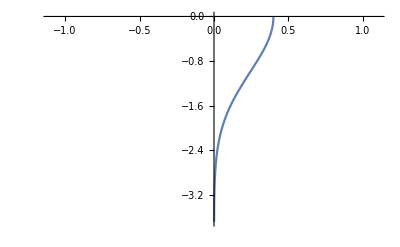

```mathematica
Plot[-√2 √Log[1/(√(2 π) x)],{x,-1.09709127110394,1.09709127110394}]
```

```mathematica
Manipulate[
Plot[
{x,-√2 √Log[1/(√(2 π) x)],(ⅇ^(-x^2/2))/(√(2 π)),(1-a)(-√2 √Log[1/(√(2 π) x)])+a ((ⅇ^(-x^2/2))/(√(2 π)))},
{x,-2,2},PlotLegends->"Expressions"],
{a,0,1}]
```

```mathematica
FindRoot[x^2+1]
```

FindRoot::argmu: FindRoot called with 1 argument; 2 or more arguments are expected.

FindRoot[x^2+1]

```mathematica
FindRoot[x^2+1,x]
```

FindRoot::fdss: Search specification x should be a list with 1 to 5 elements.

FindRoot[x^2+1,x]

```mathematica
FindRoot[x^2+1,1]
```

FindRoot::fdss: Search specification 1 should be a list with 1 to 5 elements.

FindRoot[x^2+1,1]

```mathematica
FindRoot[x^2+1,{x,1}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.}. Try perturbing the initial point(s).

{x→0.}

```mathematica
FindRoot[x^2+1,{x,1.1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→3.59175×10^-6}

```mathematica
Plot3D
```

```mathematica
Sphere[]
```

Sphere[{0,0,0}]

```mathematica
SurfaceData[Out[15],"Properties"]
```

SurfaceData::notent: Sphere[{0,0,0}] is not a known entity, class, or tag for SurfaceData. Use SurfaceData[] for a list of entities.

```mathematica
SurfaceData[Sphere[{0,0,0}],"Properties"]
```

SurfaceData::notent: Sphere[{0,0,0}] is not a known entity, class, or tag for SurfaceData. Use SurfaceData[] for a list of entities.

SurfaceData[Sphere[{0,0,0}],Properties]

```mathematica
SurfaceData["Sphere","Properties"]
```

{algebraic degree,algebraic equation,alternate names,area element,associated people,Cartesian equation,centroid of solid,Christoffel symbol of the second kind,(map) chromatic number,classes,cross sections,entity classes,Euler characteristic,filled region,coefficients of the first fundamental form,Gaussian curvature,generalized diameter,genus,3-D graphics,image,implicit Gaussian curvature,implicit mean curvature,implicit normal vector,moment of inertia tensor of solid,CDF of lengths,mean line segment length,PDF of lengths,mean curvature,metric tensor,name,number of nodes,normal vector,parameters,parametric equations,principal curvatures,number of punctures,related Wolfram Language symbols,Ricci tensor,Riemann tensor,coefficients of the second fundamental form,semialgebraic description,singular points,sport objects,surface area,variable constraints,variable descriptions,variables,vector length,volume of solid}

```mathematica
Map[SurfaceData["Sphere",#]&,SurfaceData["Sphere","Properties"]]
```

$Aborted

```mathematica
SurfaceData["Sphere","AlgebraicEquation"]
```

Function[a,Function[{x,y,z},x^2+y^2+z^2-a^2]]

```mathematica
x^2+y^2+z^2==1
```

x^2+y^2+z^2==1

```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,y,z}]
```

ContourPlot3D::argrx: ContourPlot3D called with 2 arguments; 4 arguments are expected.

ContourPlot3D[x^2+y^2+z^2==1,{x,y,z}]

```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,y,z}∈Sphere[]]
```

ContourPlot3D::idomdim: {x,y,z}∈Sphere[] does not have a valid dimension as a plotting domain.

ContourPlot3D[x^2+y^2+z^2==1,{x,y,z}∈Sphere[]]

```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x+y+z==0,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
Manipulate[
ContourPlot3D[(1-a)(x+y+z)+a(x^2+y^2+z^2)==a 1,{x,-1,1},{y,-1,1},{z,-1,1}],
{a,0,1}]
```

```mathematica
ParametricPlot3D[{x,y,0},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x,y,0},{x,-1,1},{y,-1,1}]
```

```mathematica
SurfaceData["Sphere","ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u,v,0},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u,v,0},{u,0,2π},{v,0,2π}]
```

```mathematica
{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]}
```

```mathematica
(1-a)p+a q/.{p-> {u,v,0},q->{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]}}
```

{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]}
,{u,0,2π},{v,0,2π}],
{a,0,1}]
```

```mathematica
CloudDeploy@
Manipulate[
ParametricPlot3D[
{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]}
,{u,0,2π},{v,0,2π}],
{a,0,1}]
```

CloudObject[https://www.wolframcloud.com/obj/bcdb79c8-c2f5-4010-973d-466373efdf09]